# KnotTheory` Make.nb

This notebook generates KnotTheory/init.m from the modules in src/ and KnotTheory.zip and KnotTheory.tar.gz from their sources. 
In the future this notebook will supersede the "makefile"; currently the makefile is not operational, but it is kept in the repository because it contains the list of files that go into DTCodes4Knots12To16.tar.gz and DTCodes4Knots12To16.zip which are not yet made by this notebook.
This notebook also contains some testing code.

## The Make Part

Change and execute the following cell to set the path for "trunk" on your system:

```mathematica
Switch["Dror",
"Dror", SetDirectory["C:/drorbn/projects/KnotTheory/svn/trunk"],
"Scott", SetDirectory["C:\\scott\\projects\\svn-checkouts\\KnotTheory\\trunk"],
"Radmila", SetDirectory["C:\\radmila\\KnotTheory\\trunk"]
]
```

C:\drorbn\projects\KnotTheory\svn\trunk

Most times you will not need to edit the follwing variables, so just execute the following cell to initialize them:

```mathematica
PathOf["7z"] := "c:\\Program Files\\7-Zip";
InitSources = ("src/"<>#)& /@ {
"Base.m", "Braids.m", "TubePlot.m", "DrawPD.m", "Data.m", "BraidData.m","Naming.m", "GaussCode.m", "GC2PD.m", "Indiana.m","HyperbolicVolume.m","WikiForm.m", "HOMFLYPT.m", "Kauffman.m", "Kh.m", "MorseLink.m", "DrawMorseLink.m", "ML2PD.m", "AlexanderConway.m", "VogelsAlgorithm.m", "MultivariableAlexander.m", "REngine.m", "TestRMatrix.m", "CJREngine.m", "ColouredJones.m", "HFGenus.m","KTtoLinKnot.m", "ArcPresentation.m", "HFK.m"
};
DistributionFiles= Join[
FileNames["*.m","KnotTheory"],
Select[
FileNames["*",  {"KnotTheory\\JavaKh", "KnotTheory\\WikiLink", "KnotTheory\\KnotAtlas", "KnotTheory\\scripts", "KnotTheory\\QuantumGroups", "KnotTheory\\HFK-Zurich"}, Infinity],
(FileType[#]==File) && StringFreeQ[#, "\\."]&
]
];
```

And now the action itself :

```mathematica
lines = StringReplace[#,
"---date---" -> ToString[Date[]]
]& /@ Import["src/System.mm", "Lines"];
lines = Flatten[{
lines,
{
"(* Begin source file "<>#<>"*)\n",
Import[#, "Lines"],
"(* End source file "<>#<>"*)\n\n"
}& /@ InitSources
}];
Export["KnotTheory/init.m", lines, "Lines"];
DeleteFile["KnotTheory.zip"];
Run[StringJoin[
"\""<>PathOf["7z"]<>"\\7z.exe\" ",
"a -tzip KnotTheory.zip ",
(#<>" ")& /@ DistributionFiles
]];
DeleteFile["KnotTheory.tar"];
Run[StringJoin[
"\""<>PathOf["7z"]<>"\\7z.exe\" ",
"a -ttar KnotTheory.tar ",
(#<>" ")& /@ DistributionFiles
]];
DeleteFile["KnotTheory.tar.gz"];
Run["\""<>PathOf["7z"]<>"\\7z.exe\" a -tgzip KnotTheory.tar.gz KnotTheory.tar"];
DeleteFile["KnotTheory.tar"];
```

DeleteFile::nffil: File not found during DeleteFile["KnotTheory.tar"].

## The Test Part - Computations

```mathematica
SetAttributes[Assert, HoldAll];
Assert[fact_] := Module[
{result},
If[result=fact,
True,
Print[
StringTake[ToString[Hold[fact]], {6,-2}],
" yields ", fact]
]
];
```

```mathematica
<< KnotTheory`
```

Loading KnotTheory` version of December 11, 2007, 20:47:17.2214.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
Assert[Jones[Link["L11n458"]][q] == Jones[DTCode[Link["L11n458"]]][q]]
```

KnotTheory::loading: Loading precomputed data in "Jones4Links`".

KnotTheory::loading: Loading precomputed data in "PD4Links`".

KnotTheory::credits: "The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005."

True

```mathematica
Assert[Kh[PD[Knot[3,1]]][q,t]== 1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)]
```

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

KnotTheory::credits: "The Khovanov homology program JavaKh was written by Jeremy Green in the summer of 2005 at the University of Toronto."

True

```mathematica
Assert[Last[Kh[TorusKnot[6,5], Modulus -> Null][q,t]] == q^39 t^12 ZMod[2,5]]
```

True

```mathematica
Assert[Alexander["K11a44",2][t] === {1-t+t^2}]
```

KnotTheory::loading: Loading precomputed data in "DTCode4KnotsTo11`".

KnotTheory::credits: "The program Alexander[K, r] to compute Alexander ideals was written by Jana Archibald at the University of Toronto in the summer of 2005."

True

```mathematica
Assert[
Alexander["10_99",#][t]& /@ {1,2} === {{1-4 t+10 t^2-16 t^3+19 t^4-16 t^5+10 t^6-4 t^7+t^8},{1-2 t+3 t^2-2 t^3+t^4}}
]
```

True

```mathematica
Assert[
ArcPresentation["K11n11"] === ArcPresentation[{12,2},{1,10},{3,9},{5,11},{9,12},{4,8},{2,5},{11,7},{8,6},{7,4},{10,3},{6,1}]
]
```

KnotTheory::credits: "MorseLink was added to KnotTheory` by Siddarth Sankaran\nat the University of Toronto in the summer of 2005."

True

```mathematica
Assert[
BR[ArcPresentation[
{12,2},{1,10},{3,9},{5,11},{9,12},{4,8},{2,5},{11,7},{8,6},{7,4},{10,3},{6,1}]
] === BR[4,{-1,2,3,3,-2,-1,-2,-1,2,3,3,3,2}]
]
```

KnotTheory::credits: "Vogel's algorithm was implemented by Dan Carney in the summer of 2005 at the University of Toronto."

True

```mathematica
Assert[(HFKHat[Knot[8,19]][t,m] /. m -> 1/t) == 4/t^3+1/t^2]
```

KnotTheory::credits: "The HFKHat program was written by Jean-Marie Droz in 2007 at the University of Zurich, based on methods of Anna Beliakova's arXiv:07050669."

True

```mathematica
Assert[(Plus@@ (AlternatingQ /@ AllKnots[8])) ==  3False+18 True]
```

True

## The Test Part - Graphics

```mathematica
TubePlot[TorusKnot[4,3]] // Show
```

-Graphics3D-

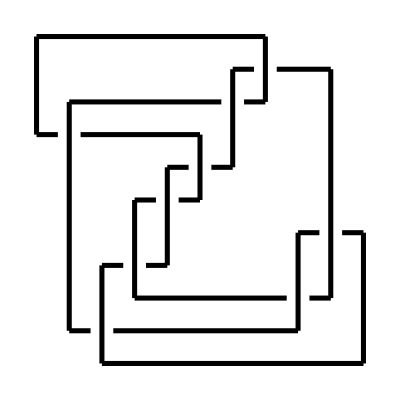

```mathematica
Draw[ArcPresentation[Knot[9,17]]]
```